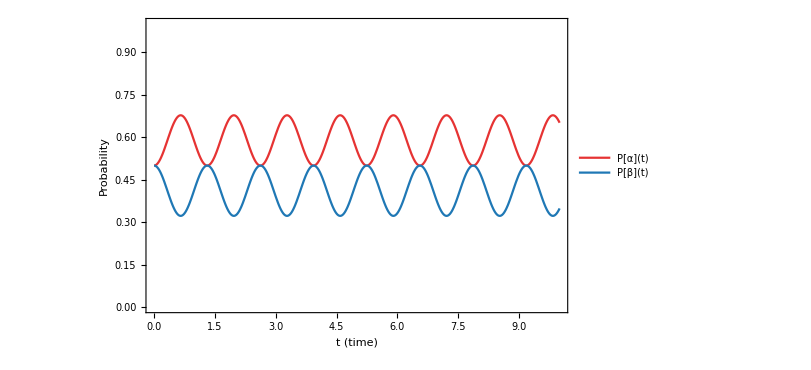

```mathematica
ClearAll["Global`*"];

(*constants*)
h=6.62607015*10^-34;
w0=2 Pi;
wm=Pi/2;

(*angle schedule*)
theta0=Pi/3;
theta[t_]:=theta0;

(*Hamiltonian*)
phi[t_]:=Mod[wm t,2 Pi];
Ω[t_]:=Sin[theta[t]];
Δ[t_]:=Cos[theta[t]];

H[t_]:=(h/2) {{w0,Ω[t] Exp[-I phi[t]]},{Ω[t] Exp[+I phi[t]],-w0}};

(*solve i h d/dt|ψ> =H|ψ>*)
sol=First@NDSolve[{I h D[{alpha[t],beta[t]},t]==H[t].{alpha[t],beta[t]},alpha[0]==1/Sqrt[2],beta[0]==1/Sqrt[2]},{alpha,beta},{t,0,10}];

(*probabilities*)
Pα[t_]:=Evaluate[Abs[alpha[t]/. sol]^2];
Pβ[t_]:=Evaluate[Abs[beta[t]/. sol]^2];

(*plot*)
colA=RGBColor[0.90,0.20,0.20];
colB=RGBColor[0.12,0.47,0.71];

pltProb=Plot[Evaluate@{Pα[t],Pβ[t]},{t,0,10},PlotStyle->{Directive[colA,Thick],Directive[colB,Thick]},Frame->True,FrameLabel->(Style[#,14]&/@{"t (time)","Probability"}),PlotRange->{0,1},ImageSize->600,PlotLegends->Placed[{"P[α](t)","P[β](t)"},Right]];

pltProb

(*numeric data used by the plot*)
tmin=0;tmax=10;nSamples=600;
ts=Subdivide[tmin,tmax,nSamples];
probData=Table[{t,Pα[t],Pβ[t]},{t,ts}];

keys={"t","Pα","Pβ"};
probAssocList=AssociationThread[keys,#]&/@probData;   (*list of <|t->...,Pα->...,Pβ->...|>*)
probDataset=Dataset[probAssocList];

(* ===Export as PDF===*)
(*dir=Quiet@Check[NotebookDirectory[],Directory[]];
pdf=FileNameJoin[{dir,"fig_probability_ab.pdf"}];
csv=FileNameJoin[{dir,"probabilities.csv"}];

Export[pdf,pltProb,"PDF"];
Export[csv,Prepend[probData,{"t","P_alpha","P_beta"}]];

Print["Saved PDF → ",pdf];
Print["Saved CSV → ",csv];*)
```